```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Directory[]
```

/Users/ninel/Server/nrvm_chbl

```mathematica
list=FileNames["./test/M*.png","",2];
```

```mathematica
FileNames["./test/*.txt","",2]
```

{}

```mathematica
{{5.4,3.074},{7.0,3.426},{8.0,3.555}}
```

```mathematica
data=Map[ToExpression,StringSplit[Import["../tnnp_chbl/test/log_6.000_0.500.txt"]]];
```

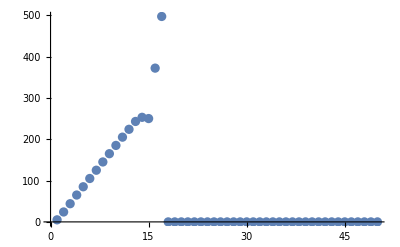

```mathematica
ListPlot[data]
```

```mathematica
fit=Fit[{Range[2001]+1499,data[[1500;;3500]]}ᵀ,{1,x},x]
```

-5.97212+0.0285644 x

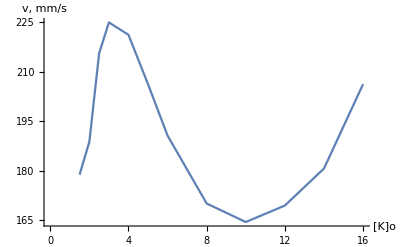

```mathematica
ListLinePlot[{{1.5,2,2.5,3,4,5,6,8,10,12,14,16},{178.75,188.75,215.625,225,221.25,206.25,190.625,170,164.375,169.375,180.625,206.25}}ᵀ,AxesLabel->{"[K]o","v, mm/s"}]
```

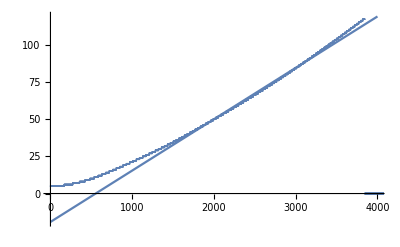

```mathematica
Show[Plot[fit,{x,1,4000}],ListPlot[data]]
```

```mathematica
ImageAssemble[{Map[Import,list[[;;;;10]]]}ᵀ]
```

-Graphics-

```mathematica
data=Map[ImageData[Import[#]]&,list[[;;]]];
```

```mathematica
Dimensions[data]
```

{1000,256,128}

```mathematica
Clear[arrtime];arrtime[dat_]:=Module[{x,y},y=Map[If[#>0.12,1,0]&,dat];x=Position[y[[2;;]]-y[[;;-2]],1]; If[Length[x]==0,1,First@Last@x]];
```

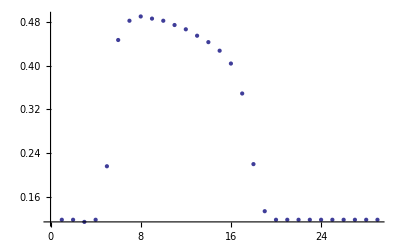

```mathematica
ListPlot[data[[57;;85,10,100]]]
```

```mathematica
F[x_]:={x[[1]],x[[2]],x[[3]]};
```

```mathematica
Manipulate[Image[data[[t]]],{t,1,700,1}]
```

Part::partd: Part specification data ⟦ 578 ⟧ is longer than depth of object.

Image::imgarray: The specified argument data ⟦ 578 ⟧ should be an array of rank 2 or 3 with machine-sized numbers.

Part::partw: Part 578 of {5, 24, 44, 65, 85, 105, 125, 145, 165, 185, 205, 224, 243, 253, 250, 372, 497, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0} does not exist.

Image::imgarray: The specified argument {5, 24, 44, 65, 85, 105, 125, 145, 165, 185, 205, 224, 243, 253, 250, 372, 497, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0} ⟦ 578 ⟧ should be an array of rank 2 or 3 with machine-sized numbers.

```mathematica
starts=(1+25(#-1))&/@Range[21];
(*starts={1,29,57,85,113,140,168,196,224,251,279};*)
ends=starts[[2;;]];
```

```mathematica
Table[Image[Table[F@ColorData["Rainbow"][(arrtime[data[[starts[[k]];;ends[[k]]-1,i,j]]]-1)/(ends[[k]]-starts[[k]])],{i,1,256},{j,1,128}]],{k,1,1(*Length@ends*)}]
```

$Aborted

```mathematica
waves=ImageAssemble@Partition[Table[Image[Table[F@ColorData["Rainbow"][(arrtime[data[[starts[[k]];;ends[[k]]-1,i,j]]]-1)/(ends[[k]]-starts[[k]]-1)],{i,1,256},{j,1,128}]],{k,1,Length@ends}],10]
```

-Graphics-

```mathematica
tab=Table[ImageSubtract[Import[list⟦n+1⟧],Import[list⟦n⟧]],{n,1,500,2}];
```

Part::partd: Part specification list ⟦ 2 ⟧ is longer than depth of object.

Import::chtype: First argument list ⟦ 2 ⟧ is not a valid file, directory, or URL specification.

Part::partd: Part specification list ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Import::chtype: First argument list ⟦ 1 ⟧ is not a valid file, directory, or URL specification.

ImageSubtract::imginv: Expecting an image or graphics instead of $Failed.

Import::chtype: First argument list ⟦ 4 ⟧ is not a valid file, directory, or URL specification.

General::stop: Further output of Import :: chtype will be suppressed during this calculation.

ImageSubtract::imginv: Expecting an image or graphics instead of $Failed.

General::stop: Further output of ImageSubtract :: imginv will be suppressed during this calculation.

```mathematica
scheme1=ImageCrop@Rasterize[Graphics[{EdgeForm[Thickness[0.005]],White,Rectangle[{0,0},{128,256}],Black,Line[{{0,168},{128,168}}],Line[{{64,168},{64,0}}]}~Join~Flatten@Table[Circle[{14+20i,242-20j},5],{i,0,5},{j,0,3}]~Join~Flatten@Table[Point[{14+20i,242-20j}],{i,0,5},{j,0,3}]~Join~Flatten@Table[Line[{{64,8+8j},{128,8+8j}}],{j,0,19}]~Join~Flatten@Table[Line[{{8i,0},{8i,168}}],{i,1,7}]],ImageSize->{256,512}+{11,11}];
```

```mathematica
512/6 //N
```

85.3333

```mathematica
scheme2=ImageCrop@Rasterize[Graphics[{EdgeForm[Thickness[0.005]],White,Rectangle[{0,0},{128,512}],Black,Line[{{0,84},{128,84}}],Line[{{0,512-84},{128,512-84}}],Line[{{64,512-84},{64,84}}]}~Join~Flatten@Table[Circle[{14+20i,501-20j},5],{i,0,5},{j,0,3}]~Join~Flatten@Table[Point[{14+20i,501-20j}],{i,0,5},{j,0,3}]~Join~Flatten@Table[Line[{{64,420-8j},{128,420-8j}}],{j,0,41}]~Join~Flatten@Table[Line[{{8i,428},{8i,84}}],{i,1,7}]~Join~Flatten@Table[Circle[{14+20i,72-20j},5],{i,0,5},{j,0,3}]~Join~Flatten@Table[Point[{14+20i,72-20j}],{i,0,5},{j,0,3}]],ImageSize->{256,1024}+{11,13}];
ImageDimensions[scheme2];
```

```mathematica
scheme3=ImageCrop@Rasterize[Graphics[{EdgeForm[Thickness[0.005]],White,Rectangle[{0,0},{128,256}],Black,Line[{{64,256},{64,0}}]}~Join~Flatten@Table[Line[{{64,248-8j},{128,248-8j}}],{j,0,30}]~Join~Flatten@Table[Line[{{8i,0},{8i,256}}],{i,1,7}]],ImageSize->{256,512}+{10.7,11}];
```

```mathematica
scheme6=ImageCrop@Rasterize[Graphics[{EdgeForm[Thickness[0.005]],White,Rectangle[{0,0},{128,1024}],Black,Line[{{64,1024},{64,0}}]}~Join~Flatten@Table[Line[{{64,1008-16j},{128,1008-16j}}],{j,0,62}]~Join~Flatten@Table[Line[{{16i,0},{16i,1024}}],{i,1,4}]],ImageSize->{128,1024}+{6.1,6.4}];
```

```mathematica
ImageDimensions[scheme6]
```

{129,1024}

```mathematica
M=25/1.5;waves=ImageAssemble@Partition[Table[ImageAdd@Table[ColorCombine@Map[ImageMultiply[ImageAdjust[tab[[Round[n]]],{1,1}],#]&,ColorData["SunsetColors"][(n-i M)/M][[#]]&/@Range[3]],{n,i M + 1,(i+1)M}],{i,0,5}],10]
```

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Graphics[Legend[ColorData["Rainbow"][1-#1]&,25," 500 ms","0 ms"]]
```

-Graphics-

```mathematica
ImageAssemble[{scheme1,waves}]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

```mathematica
ImageAssemble@Partition[Map[Import,list⟦50;;;;10⟧],10]
```

-Graphics-